```mathematica
Biarc[p1_, t1_, p2_, t2_, θ_] := Module[
{A,n1,r1,nθ, o1, n2, r2, o2, Δp, Δn, ϕ1, pq1, q1, q2, pq2, ϕ2},

n1 = Cross[t1];
n2 = Cross[t2];
nθ = {-Sin[θ], Cos[θ]};
A = Transpose[{n1-nθ, -n2+nθ}];
Δp = p2 - p1;
{r1, r2} = LinearSolve[A, Δp];

o1 = p1 + r1 n1;
o2 = p2 + r2 n2;

q1 = o1 - r1 nθ;
pq1=Normalize[q1-p1];
ϕ1=2 Sign[pq1.t1] ArcSin[Abs[pq1.n1]];
If[ϕ1 < 0, ϕ1 += 2π];

q2 = o2 - r2 nθ;
pq2 = Normalize[q2 - p2];
ϕ2 = -2 Sign[pq2.t2] ArcSin[Abs[pq2.n2]];
If[ϕ2 < 0, ϕ2 += 2π];

<|
"n1"->n1,
"o1"->o1,
"p1"->p1,
"q1"->q1,
"r1"->r1,
"t1"->t1,
"ϕ1"->ϕ1,

"n2"->n2,
"o2"->o2,
"p2"->p2,
"q2"->q2,
"r2"->r2,
"t2"->t2,
"ϕ2"->ϕ2,

"L1" -> ϕ1 Abs[r1],
"L2" -> ϕ2 Abs[r2],
"L"-> ϕ1 Abs[r1] + ϕ2 Abs[r2]
|>

]

DrawBiarc[path_] := {
Opacity[0.4],
RGBColor["#99AAB5"],
Circle[path["o1"], Abs[path["r1"]]],
Circle[path["o2"], Abs[path["r2"]]],
Opacity[1.0],
Red,
Point[path["p1"]],
Point[path["p2"]],
Point[path["q1"]],
Point[path["q2"]],
RGBColor["#7289DA"],
Line[Join[
Table[path["o1"]-path["r1"]RotationMatrix[Sign[path["r1"]]θ].path["n1"], {θ, 0, path["ϕ1"], 0.01}],
Reverse[Table[path["o2"]-path["r2"]RotationMatrix[-Sign[path["r2"]]θ].path["n2"], {θ, 0, path["ϕ2"], 0.01}]]
]]
}
```

```mathematica
Manipulate[
b = Biarc[{0, 0}, {1, 0},endpt, {Cos[zz], Sin[zz]},t];
Graphics[{
DrawBiarc[b],
Red,
Line[5{{Sin[t], 1-Cos[t]},-{Sin[t], 1-Cos[t]}}]
}, Background->DiscordGray, PlotRange->5{{-1,1}, {-1, 1}}],
{t,0,2π},
{{endpt,{3,2}},Locator},
{zz,0,2π}
]
```

```mathematica
nθ = {nθx, nθy};
n1 = {n1x, n1y};
n2 = {n2x, n2y};
Δp = {Δpx, Δpy};
A = Transpose[{n1,-n2}];
B = Transpose[{-nθ,nθ}];
{r1, r2} = FullSimplify[LinearSolve[A+B, Δp]]
```

{(-n2y Δpx+nθy Δpx+(n2x-nθx) Δpy)/(n1y (n2x-nθx)+n2y nθx-n2x nθy+n1x (-n2y+nθy)),(-n1y Δpx+nθy Δpx+(n1x-nθx) Δpy)/(n1y (n2x-nθx)+n2y nθx-n2x nθy+n1x (-n2y+nθy))}

```mathematica
RegionFunction->Function[{r1,r2},Abs[r1]>0.5 && Abs[r2] > 0.5]
```

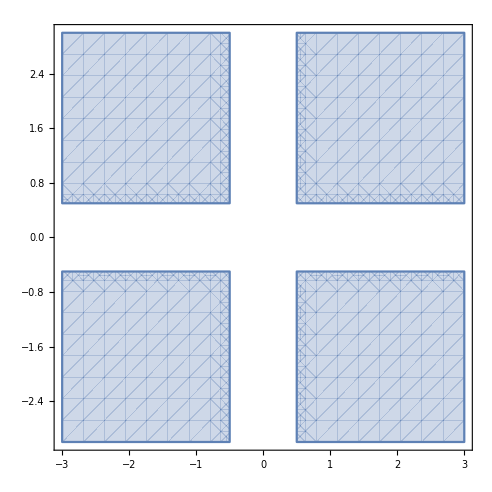

```mathematica
RegionPlot[Abs[r1]>0.5 && Abs[r2] > 0.5, {r1,-3,3},{r2,-3,3}]
```

```mathematica
dr = 300;
points = {
Flatten[Table[{-r1, -r2}, {r1, {500, 1800}}, {r2, {500, 1800}}],1],
Flatten[Table[{r1, -r2}, {r1, {500, 1800}}, {r2, {500, 1800}}],1],
Flatten[Table[{-r1, r2}, {r1, {500, 1800}}, {r2, {500, 1800}}],1],
Flatten[Table[{r1, r2}, {r1, {500, 1800}}, {r2, {500, 1800}}],1]
};
```

```mathematica
points
```

{{-500,500},{-500,1800},{-1800,500},{-1800,1800},{-500,500},{-500,1800},{-1800,500},{-1800,1800},{-500,500},{-500,1800},{-1800,500},{-1800,1800},{-500,500},{-500,1800},{-1800,500},{-1800,1800}}

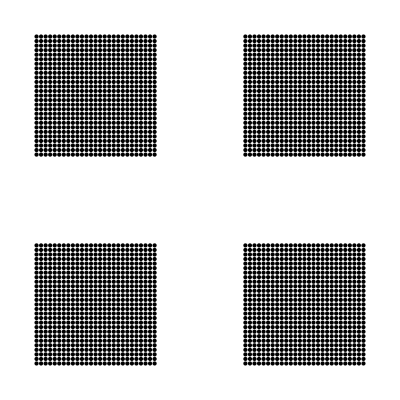

```mathematica
Manipulate[
n1={-Sin[ϕ1],Cos[ϕ1]};
n2={-Sin[ϕ2],Cos[ϕ2]};
nθ={-Sin[θ],Cos[θ]};
A=Transpose[{n1-nθ, -n2+nθ}];
Graphics[{Point /@ points, Red, Point /@ (A.#& /@ points)}],
{θ, 0, 2π},
{ϕ1, 0, 2π},
{ϕ2, 0, 2π}
]
```

```mathematica
Integrate[Exp[-x^2],{x,-∞,∞},Assumptions->{a>0}]
```

√π